```mathematica
link=Install[LinkConnect["33455@192.168.150.128,39549@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.7],ωbhe=7.5*Sqrt[0.2],ωe=150,
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=3.9,wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

```mathematica
sol=With[{k=Range[4.0,5.5,0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[3.44,0.029] (1+0.0001 I {0,1,2}),MaxIterations->100]];
ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[17]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["2.txt",gama];
```

{2.00337-0.00373934 ⅈ,2.00346-0.00380301 ⅈ,2.00354-0.00385359 ⅈ,2.00361-0.00388897 ⅈ,2.00366-0.00390592 ⅈ,2.00368-0.00390028 ⅈ,2.00367-0.00386579 ⅈ,2.00361-0.00379325 ⅈ,2.00349-0.00366936 ⅈ,2.00332-0.0034766 ⅈ,2.00312-0.0032024 ⅈ,2.00294-0.00285006 ⅈ,2.00279-0.00243635 ⅈ,2.0027-0.00197645 ⅈ,2.00266-0.00147434 ⅈ,2.00269-0.000921863 ⅈ,2.0028-0.000301938 ⅈ,2.003+0.000413339 ⅈ,2.0033+0.00126538 ⅈ,2.00376+0.00231846 ⅈ,2.00443+0.00368014 ⅈ,2.00544+0.00554247 ⅈ,2.00705+0.00829207 ⅈ,2.00967+0.0127901 ⅈ,2.01493+0.0209579 ⅈ,2.02932+0.0319642 ⅈ}

{2.00337-0.00373934 ⅈ,2.00346-0.00380301 ⅈ,2.00354-0.00385359 ⅈ,2.00361-0.00388897 ⅈ,2.00366-0.00390592 ⅈ,2.00368-0.00390028 ⅈ,2.00367-0.00386579 ⅈ,2.00361-0.00379325 ⅈ,2.00349-0.00366936 ⅈ,2.00332-0.0034766 ⅈ,2.00312-0.0032024 ⅈ,2.00294-0.00285006 ⅈ,2.00279-0.00243635 ⅈ,2.0027-0.00197645 ⅈ,2.00266-0.00147434 ⅈ,2.00269-0.000921863 ⅈ,2.0028-0.000301938 ⅈ,2.003+0.000413339 ⅈ,2.0033+0.00126538 ⅈ,2.00376+0.00231846 ⅈ,2.00443+0.00368014 ⅈ,2.00544+0.00554247 ⅈ,2.00705+0.00829207 ⅈ,2.00967+0.0127901 ⅈ,2.01493+0.0209579 ⅈ,2.02932+0.0319642 ⅈ,1.98365+0.0209924 ⅈ,1.9789+0.0166067 ⅈ,1.97619+0.0125336 ⅈ,1.97442+0.00878592 ⅈ,1.97349+0.00507597 ⅈ,1.97363+0.00128592 ⅈ,1.97557-0.00216689 ⅈ,1.97868-0.00333658 ⅈ,1.98073-0.00299777 ⅈ,1.98197-0.00242564 ⅈ,1.98277-0.00187202 ⅈ,1.98332-0.00138166 ⅈ,1.9837-0.000960378 ⅈ,1.98398-0.000604762 ⅈ,1.98416-0.000309434 ⅈ,1.98428-0.0000688846 ⅈ,1.98435+0.000121877 ⅈ,1.98437+0.000268197 ⅈ,1.98435+0.000376244 ⅈ,1.98439+0.000446523 ⅈ,1.98421+0.000499461 ⅈ,1.9841+0.000523224 ⅈ,1.98398+0.000527656 ⅈ,1.98383+0.000517161 ⅈ,1.98367+0.000495344 ⅈ}

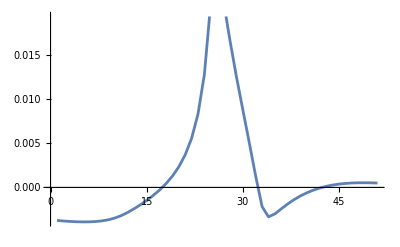

```mathematica
sol1=With[{k=Range[2.75,1.5,-0.05],wna=88Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[2.8,4.0,0.05],wna=89Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["89heim-2,1.5-4.0.csv",Im[sol]];

Export["88here-4,5.5-8.0.csv",Re[sol]];
```